```mathematica
ClearAll["Global`*"]
system={x''[t]==-y'[t]w[t],y''[t]==x'[t]w[t],w'[t]==ϵ}
initialv={x'[0]==0,y'[0]==s}
initial={x[0]==0,y[0]==0,w[0]==0}
```

{x''[t]==-w[t] y'[t],y''[t]==w[t] x'[t],w'[t]==ϵ}

{x'[0]==0,y'[0]==s}

{x[0]==0,y[0]==0,w[0]==0}

```mathematica
equations = Join[system, initialv, initial]
res = DSolve[equations, {x,y,w},{t, 0, 10}]
```

{x''[t]==-w[t] y'[t],y''[t]==w[t] x'[t],w'[t]==ϵ,x'[0]==0,y'[0]==s,x[0]==0,y[0]==0,w[0]==0}

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 1/(√π √ϵ) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 2 ArcCos[Cos[1^2/(2 ϵ)]] == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{x→Function[{t},-(√π s FresnelS[(t √ϵ)/(√π)])/(√ϵ)],y→Function[{t},(√π s FresnelC[(t √ϵ)/(√π)])/(√ϵ)],w→Function[{t},t ϵ]}}

```mathematica
sx[t_]=D[x[t]/.res[[1]],t]
sy[t_]=D[y[t]/.res[[1]],t]
```

-s Sin[(t^2 ϵ)/2]

s Cos[(t^2 ϵ)/2]

```mathematica
xr[t_]:=Evaluate[x[t]/.res[[1]]]
yr[t_]:=Evaluate[y[t]/.res[[1]]]
ϵ=0.1
s=2.0
```

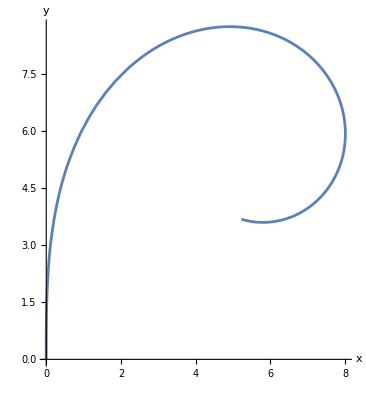

```mathematica
ParametricPlot[{xr[t],yr[t]},{t,0,10},AspectRatio->Automatic,AxesLabel->{"x","y"}]
```